```mathematica
(* The Base directory when working on the lab computer *)
dropBoxOn=FileNameJoin[{"Dropbox","00School","research","DataRuns"}];
labComp=FileNameJoin[{"C:","Users","kahrendsen2",dropBoxOn}];
homeComp=FileNameJoin[{"/","home","karl",dropBoxOn}];
(* Good graphing setup *)
labelSize=18;
(* The folder that contains the different data runs to analyze, this folder contains subfolders with 
individual runs.*)
dataFolder=FileNameJoin[{labComp}]
SetDirectory[dataFolder];
(* Make a list of directories to easily select the folder you would like to work with.*)
directories=Select[FileNames["*","",1],DirectoryQ];
For[i=1,i<=Length[directories],i++,
WriteString["stdout",i -> directories[[i]],"\n"];]
```

C:\Users\kahrendsen2\Dropbox\00School\research\DataRuns

1 -> 15-06-09_USBCounterError
2 -> 15-07-06mockPolarizationData
3 -> 16-01-14
4 -> 16-01-21_Data
5 -> 16-05-25_PolarizationData
6 -> 16-07-06_PolarizationData
7 -> 16-08-04_PolarizationData
8 -> 16-08-07_HeliumTargetPictures
9 -> 16-08-09_PolarizationData
10 -> 16-10-17_polarimeter
11 -> 16-10-27_DataReport
12 -> 16-11-03_faradayRotation
13 -> 16-11-07_faradayRotation
14 -> 16-11-18_faradayRotation
15 -> 16-12-09_faradayRotation
16 -> 17-01-31
17 -> 17-02-17_plusMinus
18 -> 17-03-06_PlusMinusWavemeter
19 -> 17-03-10_non-RbFaradayRotation
20 -> 17-03-15_AimingFor5e12
21 -> 17-03-15_wavemeterNoRb
22 -> 17-03-28
23 -> 17-03-29_pumpLaserFindingCircular
24 -> 17-03-30_WavemeterReliability
25 -> 17-04-04_polarization
26 -> 17-04-06_polarization
27 -> 17-04-07_wmReliability
28 -> 17-04-18
29 -> 17-04-18_polarization
30 -> 17-04-22
31 -> 17-04-25_ProbePolarizationDriftOpenChamber
32 -> 17-04-30_laserReport
33 -> 17-05-17_DirtyGunRun
34 -> 17-05-18_ProbeDrift
35 -> 17-05-19_BetterLaser
36 -> 17-05-24_SimplifiedPolarization
37 -> 17-05-25_LaserProfiling
38 -> 17-06-02
39 -> 17-06-06_IntensityOfProbeStudy
40 -> 17-06-11
41 -> 17-06-13
42 -> 17-06-16
43 -> 17-06-17
44 -> 17-06-25
45 -> 17-07-01_nRbVsBufferGasAnalysis
46 -> 17-07-01_PumpLaserAnalysis
47 -> 17-07-03_lowerNRb_BGPStudy
48 -> 17-07-03_ProbeDrift
49 -> 17-07-03_pumpBroadening
50 -> 17-07-06_lotsOfProbeMeasurements
51 -> 17-07-06_MagneticField
52 -> 17-07-06_probePower
53 -> 17-07-12_polVsPumpPower
54 -> 17-08-01_rgaInitialScans
55 -> 17-08-03_redoingSystemDiagnostic
56 -> 17-08-06_probeDrift
57 -> 17-08-18_furtherPolarizationStudy
58 -> 17-08-19_furtherPolarizationStudy2
59 -> 17-08-22_furtherPolarizationStudyFoundLeak
60 -> 17-08-29_BvsProbePower_probeDetuneVsMagnetRot
61 -> 17-09-05_Polarizations_100mTBGP
62 -> 17-09-20
63 -> 17-10-03_ElectronGun
64 -> 17-10-16_ElectronGun
65 -> 17-10-24_UnpolarizedPolarization
66 -> 17-10-26_24And30eVRuns
67 -> 17-10-28_24and30eVRedux
68 -> 17-11-04_MoreUnpolarizedRuns
69 -> 17-11-06_UnpolarizedRuns2
70 -> 17-11-15_BalancedPhotoDetector
71 -> 17-11-18_SystemDiagnosis
72 -> 17-12-18_SystemDiagnosis
73 -> 17-12-20_PolarizingElectrons
74 -> 18-01-03_PolarizingElectrons
75 -> 18-01-04_PolarizingElectrons
76 -> 18-01-10_ChamberWarming
77 -> 18-01-11_SystemDiagnostics
78 -> 18-01-12_recreatingPolFigure
79 -> 18-01-13_recreatingPolFigureIncreasedT
80 -> 18-01-16_morePolarization
81 -> 18-01-20_electronPolarization
82 -> 18-01-25_excitationFunctions
83 -> 18-01-28_bufferGasPressureVsCounts
84 -> 18-01-28_hayesReproduction
85 -> 18-02-12_polarizedElectrons
86 -> 18-02-13
87 -> 18-02-15_addtlBGP
88 -> dataDump
89 -> pumpQWP
90 -> wavemeterOffsets

```mathematica
(* set rootFolder to the folder name containing the RbPolarization Files *)
rootFolder=FileNameJoin[{dataFolder,directories[[86]],"data"}];
SetDirectory[rootFolder];
(* Obtain the filename of the absorption data *)
scanFiles=FileNames["FDayScan"~~RegularExpression[".{25,25}"]~~"Analysis.dat"];
Length[scanFiles]
For[i=1,i<=Length[scanFiles],i+=2,
WriteString["stdout",i -> scanFiles[[i]], "    ",i+1->scanFiles[[i+1]],"\n"];]
```

97

1 -> FDayScan2018-02-13_011148RotationAnalysis.dat    2 -> FDayScan2018-02-13_011430RotationAnalysis.dat
3 -> FDayScan2018-02-13_011711RotationAnalysis.dat    4 -> FDayScan2018-02-13_011952RotationAnalysis.dat
5 -> FDayScan2018-02-13_044852RotationAnalysis.dat    6 -> FDayScan2018-02-13_045339RotationAnalysis.dat
7 -> FDayScan2018-02-13_045826RotationAnalysis.dat    8 -> FDayScan2018-02-13_050312RotationAnalysis.dat
9 -> FDayScan2018-02-13_164412RotationAnalysis.dat    10 -> FDayScan2018-02-13_164859RotationAnalysis.dat
11 -> FDayScan2018-02-13_165346RotationAnalysis.dat    12 -> FDayScan2018-02-13_165832RotationAnalysis.dat
13 -> FDayScan2018-02-13_180318RotationAnalysis.dat    14 -> FDayScan2018-02-13_180805RotationAnalysis.dat
15 -> FDayScan2018-02-13_181251RotationAnalysis.dat    16 -> FDayScan2018-02-13_181738RotationAnalysis.dat
17 -> FDayScan2018-02-13_225034RotationAnalysis.dat    18 -> FDayScan2018-02-13_225521RotationAnalysis.dat
19 -> FDayScan2018-02-13_230007RotationAnalysis.dat    20 -> FDayScan2018-02-13_230454RotationAnalysis.dat
21 -> FDayScan2018-02-13_231355RotationAnalysis.dat    22 -> FDayScan2018-02-13_231842RotationAnalysis.dat
23 -> FDayScan2018-02-13_232328RotationAnalysis.dat    24 -> FDayScan2018-02-13_232814RotationAnalysis.dat
25 -> FDayScan2018-02-14_040109RotationAnalysis.dat    26 -> FDayScan2018-02-14_040556RotationAnalysis.dat
27 -> FDayScan2018-02-14_041044RotationAnalysis.dat    28 -> FDayScan2018-02-14_041531RotationAnalysis.dat
29 -> FDayScan2018-02-14_042432RotationAnalysis.dat    30 -> FDayScan2018-02-14_042922RotationAnalysis.dat
31 -> FDayScan2018-02-14_043408RotationAnalysis.dat    32 -> FDayScan2018-02-14_043856RotationAnalysis.dat
33 -> FDayScan2018-02-14_091152RotationAnalysis.dat    34 -> FDayScan2018-02-14_091638RotationAnalysis.dat
35 -> FDayScan2018-02-14_092124RotationAnalysis.dat    36 -> FDayScan2018-02-14_092611RotationAnalysis.dat
37 -> FDayScan2018-02-14_112735RotationAnalysis.dat    38 -> FDayScan2018-02-14_114152RotationAnalysis.dat
39 -> FDayScan2018-02-14_114639RotationAnalysis.dat    40 -> FDayScan2018-02-14_115126RotationAnalysis.dat
41 -> FDayScan2018-02-14_115613RotationAnalysis.dat    42 -> FDayScan2018-02-14_125647RotationAnalysis.dat
43 -> FDayScan2018-02-14_130134RotationAnalysis.dat    44 -> FDayScan2018-02-14_130631RotationAnalysis.dat
45 -> FDayScan2018-02-14_131119RotationAnalysis.dat    46 -> FDayScan2018-02-14_135941RotationAnalysis.dat
47 -> FDayScan2018-02-14_140429RotationAnalysis.dat    48 -> FDayScan2018-02-14_140916RotationAnalysis.dat
49 -> FDayScan2018-02-14_141403RotationAnalysis.dat    50 -> FDayScan2018-02-14_160244RotationAnalysis.dat
51 -> FDayScan2018-02-14_160734RotationAnalysis.dat    52 -> FDayScan2018-02-14_161226RotationAnalysis.dat
53 -> FDayScan2018-02-14_161712RotationAnalysis.dat    54 -> FDayScan2018-02-14_190410RotationAnalysis.dat
55 -> FDayScan2018-02-14_190857RotationAnalysis.dat    56 -> FDayScan2018-02-14_191343RotationAnalysis.dat
57 -> FDayScan2018-02-14_191833RotationAnalysis.dat    58 -> FDayScan2018-02-14_201518RotationAnalysis.dat
59 -> FDayScan2018-02-14_202005RotationAnalysis.dat    60 -> FDayScan2018-02-14_202451RotationAnalysis.dat
61 -> FDayScan2018-02-14_202937RotationAnalysis.dat    62 -> FDayScan2018-02-14_231634RotationAnalysis.dat
63 -> FDayScan2018-02-14_232121RotationAnalysis.dat    64 -> FDayScan2018-02-14_232607RotationAnalysis.dat
65 -> FDayScan2018-02-14_233053RotationAnalysis.dat    66 -> FDayScan2018-02-15_015409RotationAnalysis.dat
67 -> FDayScan2018-02-15_015855RotationAnalysis.dat    68 -> FDayScan2018-02-15_020343RotationAnalysis.dat
69 -> FDayScan2018-02-15_020830RotationAnalysis.dat    70 -> FDayScan2018-02-15_064230RotationAnalysis.dat
71 -> FDayScan2018-02-15_064716RotationAnalysis.dat    72 -> FDayScan2018-02-15_065204RotationAnalysis.dat
73 -> FDayScan2018-02-15_065650RotationAnalysis.dat    74 -> FDayScan2018-02-15_161139RotationAnalysis.dat
75 -> FDayScan2018-02-15_161633RotationAnalysis.dat    76 -> FDayScan2018-02-15_162126RotationAnalysis.dat
77 -> FDayScan2018-02-15_162621RotationAnalysis.dat    78 -> FDayScan2018-02-15_182309RotationAnalysis.dat
79 -> FDayScan2018-02-15_182803RotationAnalysis.dat    80 -> FDayScan2018-02-15_183258RotationAnalysis.dat
81 -> FDayScan2018-02-15_183751RotationAnalysis.dat    82 -> FDayScan2018-02-15_193809RotationAnalysis.dat
83 -> FDayScan2018-02-15_194305RotationAnalysis.dat    84 -> FDayScan2018-02-15_194758RotationAnalysis.dat
85 -> FDayScan2018-02-15_195250RotationAnalysis.dat    86 -> FDayScan2018-02-15_214935RotationAnalysis.dat
87 -> FDayScan2018-02-15_215431RotationAnalysis.dat    88 -> FDayScan2018-02-15_215927RotationAnalysis.dat
89 -> FDayScan2018-02-15_220419RotationAnalysis.dat    90 -> FDayScan2018-02-15_230444RotationAnalysis.dat
91 -> FDayScan2018-02-15_230936RotationAnalysis.dat    92 -> FDayScan2018-02-15_231432RotationAnalysis.dat
93 -> FDayScan2018-02-15_231928RotationAnalysis.dat    94 -> FDayScan2018-02-16_011615RotationAnalysis.dat
95 -> FDayScan2018-02-16_012112RotationAnalysis.dat    96 -> FDayScan2018-02-16_012608RotationAnalysis.dat
97 -> FDayScan2018-02-16_013104RotationAnalysis.dat    98 -> {FDayScan2018-02-13_011148RotationAnalysis.dat, FDayScan2018-02-13_011430RotationAnalysis.dat, FDayScan2018-02-13_011711RotationAnalysis.dat, FDayScan2018-02-13_011952RotationAnalysis.dat, FDayScan2018-02-13_044852RotationAnalysis.dat, FDayScan2018-02-13_045339RotationAnalysis.dat, FDayScan2018-02-13_045826RotationAnalysis.dat, FDayScan2018-02-13_050312RotationAnalysis.dat, FDayScan2018-02-13_164412RotationAnalysis.dat, FDayScan2018-02-13_164859RotationAnalysis.dat, FDayScan2018-02-13_165346RotationAnalysis.dat, FDayScan2018-02-13_165832RotationAnalysis.dat, FDayScan2018-02-13_180318RotationAnalysis.dat, FDayScan2018-02-13_180805RotationAnalysis.dat, FDayScan2018-02-13_181251RotationAnalysis.dat, FDayScan2018-02-13_181738RotationAnalysis.dat, FDayScan2018-02-13_225034RotationAnalysis.dat, FDayScan2018-02-13_225521RotationAnalysis.dat, FDayScan2018-02-13_230007RotationAnalysis.dat, FDayScan2018-02-13_230454RotationAnalysis.dat, FDayScan2018-02-13_231355RotationAnalysis.dat, FDayScan2018-02-13_231842RotationAnalysis.dat, FDayScan2018-02-13_232328RotationAnalysis.dat, FDayScan2018-02-13_232814RotationAnalysis.dat, FDayScan2018-02-14_040109RotationAnalysis.dat, FDayScan2018-02-14_040556RotationAnalysis.dat, FDayScan2018-02-14_041044RotationAnalysis.dat, FDayScan2018-02-14_041531RotationAnalysis.dat, FDayScan2018-02-14_042432RotationAnalysis.dat, FDayScan2018-02-14_042922RotationAnalysis.dat, FDayScan2018-02-14_043408RotationAnalysis.dat, FDayScan2018-02-14_043856RotationAnalysis.dat, FDayScan2018-02-14_091152RotationAnalysis.dat, FDayScan2018-02-14_091638RotationAnalysis.dat, FDayScan2018-02-14_092124RotationAnalysis.dat, FDayScan2018-02-14_092611RotationAnalysis.dat, FDayScan2018-02-14_112735RotationAnalysis.dat, FDayScan2018-02-14_114152RotationAnalysis.dat, FDayScan2018-02-14_114639RotationAnalysis.dat, FDayScan2018-02-14_115126RotationAnalysis.dat, FDayScan2018-02-14_115613RotationAnalysis.dat, FDayScan2018-02-14_125647RotationAnalysis.dat, FDayScan2018-02-14_130134RotationAnalysis.dat, FDayScan2018-02-14_130631RotationAnalysis.dat, FDayScan2018-02-14_131119RotationAnalysis.dat, FDayScan2018-02-14_135941RotationAnalysis.dat, FDayScan2018-02-14_140429RotationAnalysis.dat, FDayScan2018-02-14_140916RotationAnalysis.dat, FDayScan2018-02-14_141403RotationAnalysis.dat, FDayScan2018-02-14_160244RotationAnalysis.dat, FDayScan2018-02-14_160734RotationAnalysis.dat, FDayScan2018-02-14_161226RotationAnalysis.dat, FDayScan2018-02-14_161712RotationAnalysis.dat, FDayScan2018-02-14_190410RotationAnalysis.dat, FDayScan2018-02-14_190857RotationAnalysis.dat, FDayScan2018-02-14_191343RotationAnalysis.dat, FDayScan2018-02-14_191833RotationAnalysis.dat, FDayScan2018-02-14_201518RotationAnalysis.dat, FDayScan2018-02-14_202005RotationAnalysis.dat, FDayScan2018-02-14_202451RotationAnalysis.dat, FDayScan2018-02-14_202937RotationAnalysis.dat, FDayScan2018-02-14_231634RotationAnalysis.dat, FDayScan2018-02-14_232121RotationAnalysis.dat, FDayScan2018-02-14_232607RotationAnalysis.dat, FDayScan2018-02-14_233053RotationAnalysis.dat, FDayScan2018-02-15_015409RotationAnalysis.dat, FDayScan2018-02-15_015855RotationAnalysis.dat, FDayScan2018-02-15_020343RotationAnalysis.dat, FDayScan2018-02-15_020830RotationAnalysis.dat, FDayScan2018-02-15_064230RotationAnalysis.dat, FDayScan2018-02-15_064716RotationAnalysis.dat, FDayScan2018-02-15_065204RotationAnalysis.dat, FDayScan2018-02-15_065650RotationAnalysis.dat, FDayScan2018-02-15_161139RotationAnalysis.dat, FDayScan2018-02-15_161633RotationAnalysis.dat, FDayScan2018-02-15_162126RotationAnalysis.dat, FDayScan2018-02-15_162621RotationAnalysis.dat, FDayScan2018-02-15_182309RotationAnalysis.dat, FDayScan2018-02-15_182803RotationAnalysis.dat, FDayScan2018-02-15_183258RotationAnalysis.dat, FDayScan2018-02-15_183751RotationAnalysis.dat, FDayScan2018-02-15_193809RotationAnalysis.dat, FDayScan2018-02-15_194305RotationAnalysis.dat, FDayScan2018-02-15_194758RotationAnalysis.dat, FDayScan2018-02-15_195250RotationAnalysis.dat, FDayScan2018-02-15_214935RotationAnalysis.dat, FDayScan2018-02-15_215431RotationAnalysis.dat, FDayScan2018-02-15_215927RotationAnalysis.dat, FDayScan2018-02-15_220419RotationAnalysis.dat, FDayScan2018-02-15_230444RotationAnalysis.dat, FDayScan2018-02-15_230936RotationAnalysis.dat, FDayScan2018-02-15_231432RotationAnalysis.dat, FDayScan2018-02-15_231928RotationAnalysis.dat, FDayScan2018-02-16_011615RotationAnalysis.dat, FDayScan2018-02-16_012112RotationAnalysis.dat, FDayScan2018-02-16_012608RotationAnalysis.dat, FDayScan2018-02-16_013104RotationAnalysis.dat}[[98]]

Part::partw: Part 98 of {FDayScan2018-02-13_011148RotationAnalysis.dat,FDayScan2018-02-13_011430RotationAnalysis.dat,FDayScan2018-02-13_011711RotationAnalysis.dat,FDayScan2018-02-13_011952RotationAnalysis.dat,FDayScan2018-02-13_044852RotationAnalysis.dat,FDayScan2018-02-13_045339RotationAnalysis.dat,FDayScan2018-02-13_045826RotationAnalysis.dat,«38»,FDayScan2018-02-14_135941RotationAnalysis.dat,FDayScan2018-02-14_140429RotationAnalysis.dat,FDayScan2018-02-14_140916RotationAnalysis.dat,FDayScan2018-02-14_141403RotationAnalysis.dat,FDayScan2018-02-14_160244RotationAnalysis.dat,«47»} does not exist.

16.8

16.9

27.1557-0.0670937 x+0.196137 x^2

0.0000770372

{{32.5186,0.349444},{32.0204,0.349832},{31.4986,0.349908},{31.0716,0.349726},{30.5024,0.349232},{17.0774,0.350508},{16.0812,0.350687},{15.4171,0.350767},{14.6581,0.350632},{13.8517,0.351199},{13.1402,0.350638},{12.4287,0.351415},{11.6697,0.350756},{10.9582,0.352164},{10.2467,0.351819},{9.4877,0.352993},{8.77618,0.353011},{8.01724,0.355479},{7.25829,0.359295},{6.49935,0.395816}}

{{32.8269,0.348535},{32.3051,0.349264},{31.8781,0.348433},{31.3088,0.349497},{30.8344,0.34985},{17.3146,0.349258},{16.4133,0.348422},{15.6543,0.346771},{14.9902,0.346928},{14.2786,0.347768},{13.5197,0.347263},{12.8081,0.347395},{12.0492,0.34765},{11.2902,0.347628},{10.5787,0.347441},{9.86718,0.347718},{9.06079,0.346867},{8.30184,0.348735},{7.63776,0.349485},{6.83139,0.36208}}

{{32.8744,0.349371},{32.4,0.3502},{31.9256,0.349846},{31.4512,0.349079},{30.8344,0.349246},{17.4569,0.351497},{16.5081,0.351438},{15.7966,0.353208},{15.0851,0.354334},{14.3735,0.354996},{13.5671,0.354695},{12.8556,0.355947},{12.1085,0.355132},{11.3851,0.356202},{10.6261,0.356703},{9.89428,0.358954},{9.15566,0.360941},{8.31932,0.362258},{7.53915,0.365087},{6.73652,0.379378}}

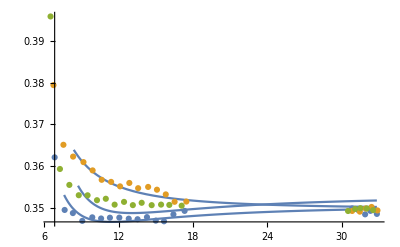

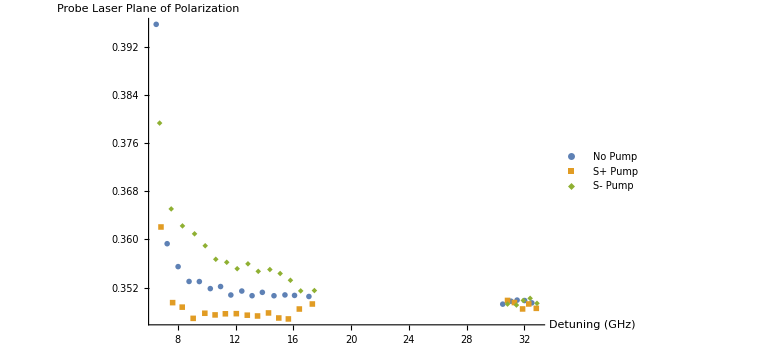

-Graphics-

```mathematica
rotationAnalysisData=Import[FileNameJoin[{rootFolder,scanFiles[[noPumpFileNumber]]}],"tsv"];
rotationAnalysisData=StripFaradayData[rotationAnalysisData];
rotationAnalysisData=FillInMissedValues[rotationAnalysisData,2,1];
rotationAnalysisData=Take[rotationAnalysisData,All,{2,-1}];
noPump=ConvertFDayDegreeToRadian[ConvertFDayWavelengthToDetune[rotationAnalysisData]]


rotationAnalysisData=Import[FileNameJoin[{rootFolder,scanFiles[[sPlusPumpFileNumber]]}],"tsv"];
rotationAnalysisData=StripFaradayData[rotationAnalysisData];
rotationAnalysisData=FillInMissedValues[rotationAnalysisData,2,1];
rotationAnalysisData=Take[rotationAnalysisData,All,{2,-1}];
sPlusPump=ConvertFDayDegreeToRadian[ConvertFDayWavelengthToDetune[rotationAnalysisData]]


rotationAnalysisData=Import[FileNameJoin[{rootFolder,scanFiles[[sMinusPumpFileNumber]]}],"tsv"];
rotationAnalysisData=StripFaradayData[rotationAnalysisData];
rotationAnalysisData=FillInMissedValues[rotationAnalysisData,2,1];
rotationAnalysisData=Take[rotationAnalysisData,All,{2,-1}];
sMinusPump=ConvertFDayDegreeToRadian[ConvertFDayWavelengthToDetune[rotationAnalysisData]]

{detune,θp}=Transpose[sPlusPump];
{detune2,θm}=Transpose[sMinusPump];

noPumpModel=NonlinearModelFit[Normal[noPump],modelA4,{{a1,1},{a2,1},{θ0,.35}},δ];
noPumpPlot=Plot[noPumpModel[δ],{δ,Min[detune],Max[detune]}];
Show[noPumpPlot,ListPlot[noPump]];

sPlusModel=NonlinearModelFit[Normal[sPlusPump],modelA4,{{a1,1},{a2,1},{θ0,.35}},δ];
sPlusPlot=Plot[sPlusModel[δ],{δ,Min[detune],Max[detune]}];
Show[sPlusPlot,ListPlot[sPlusPump]];

sMinusModel=NonlinearModelFit[Normal[sMinusPump],modelA4,{{a1,1},{a2,1},{θ0,.35}},δ];
sMinusPlot=Plot[sMinusModel[δ],{δ,Min[detune],Max[detune]}];
Show[sMinusPlot,ListPlot[sMinusPump]];

Show[sPlusPlot,sMinusPlot,noPumpPlot,ListPlot[{sPlusPump,sMinusPump,noPump}],PlotRange->All]

pumpDifference=Transpose[{detune-detuningOffset,θp-θm}];
differencePlot=ListPlot[Legended[pumpDifference,"(S+) - (S-)"],AxesLabel->{"Detuning (GHz)","Linear Pol. Angle"},PlotRange->All,LabelStyle->18,PlotMarkers->{Automatic,Large},ImageSize->Large];
Rasterize[differencePlot];
allPlot=ListPlot[{Legended[noPump,"No Pump"],Legended[sPlusPump,"S+ Pump"],Legended[sMinusPump,"S- Pump"]},PlotRange->All,LabelStyle->18,PlotMarkers->{Automatic,Large},ImageSize->Large,AxesLabel->{"Detuning (GHz)","Probe Laser\nPlane of Polarization"}]
Rasterize[allPlot]
```

FittedModel[0.00385526-0.13198 x]

Integrated Magnetic Field (T*m):

0.0000770372

Number Density (cm^-3):

3.2×10^12

Slope:

-0.13198

Polarization:

-0.00162479

Polarization Uncertainty:

0.000203582

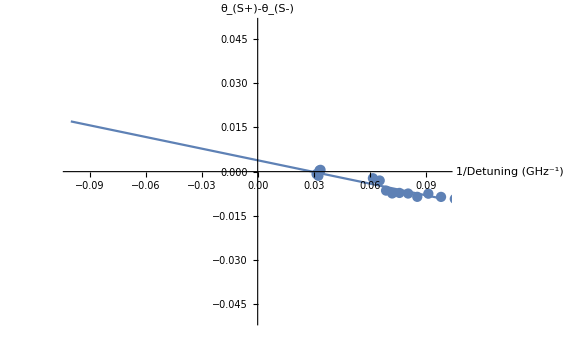

```mathematica
(* Calculates fit for data *)
(* Removes datapoints that wrapped in rotation *)
lowerBoundDetuning=8;
upperBoundDetuning=35;

pumpDiff=Dataset[pumpDifference];
pumpDiff=pumpDiff[Select[Abs[#[[1]]]<upperBoundDetuning&]];
pumpDiff=pumpDiff[Select[Abs[#[[1]]]>lowerBoundDetuning&]];
pumpDiff=Normal[pumpDiff];
labelSize=18;

Clear[a,b,c,d,e]

(* Calculates fit for polarization *)
{detune,δθ}=Transpose[pumpDiff];
newThing=Transpose[{1/detune,δθ}];
lm=LinearModelFit[newThing,x,x]
polPlot=Plot[lm[x],{x,-.1,.1}];

slope=lm["BestFitParameters"][[2]];

Cpar=1.2692*^-11;
c=2.99792458*^8;
re=2.8179*^-15;
fge=0.34231;
k=4/3;
Print["Integrated Magnetic Field (T*m):"]
BdotL
μ=9.2740*^-24;
h=6.6261*^-34;
ν0=377107.463;
conversionFactor=h/(BdotL*c*re*fge*k*μ)*10^18*10^-6;(*Conversion Factor is in 1/(Hz)^2, so we need *10^18 to convert to 1/(GHz)^2*)

Print["Number Density (cm^-3):"]
n=3.2*^12
Print["Slope:"];
Print[slope];
Print["Polarization:"]
pol=slope/(Cpar*n*2)
σSlope=lm["ParameterErrors"][[2]];
σDensity=3*^11;
Print["Polarization Uncertainty:"]
σp=Sqrt[pol^2*((σSlope/slope)^2+(σDensity/n)^2)]
Show[{ListPlot[newThing],polPlot},AxesOrigin-> {0,0},PlotRange->{{-.1,.1},{-.05,.05}},AxesLabel->{"1/Detuning\n(GHz^-1)","θ_(S+)-θ_(S-)"},LabelStyle->labelSize,ImageSize->Large]
```

## Define a function which takes two file names as an argument and outputs the polarization data related to those three faradayRotation files.

```mathematica
GetPolarization[fileName1_,fileName2_]:=Module[{},
rotationAnalysisData=Import[FileNameJoin[{rootFolder,fileName1}],"tsv"];
rotationAnalysisData=Import[FileNameJoin[{rootFolder,fileName2}],"tsv"];

];
```

```mathematica
GetCommentLine[file_,lineNumber_]:=Module[{},
file];
```

```mathematica
AddFileToMatrix[fileName_,dataset_]:=Module[{rotationAnalysisData,header,headerT,entry,data},
If[Length[dataset]<1,
rotationAnalysisData=Import[fileName,"Table","FieldSeparators"-> "\t"];
header=Take[rotationAnalysisData,{1,-3},All];
data=Take[rotationAnalysisData,{-2,-1},All];

headerT[[1]]=StringReplace[headerT[[1]],"#"->""];
headerT[[1]]=StringReplace[headerT[[1]],":"->""];
header=Transpose[headerT];

alldata=Transpose[Join[header,Transpose[data]]];
Append[dataset,entry];,


];
CreateDatasetFromNamedColumns[matrixWithNamedColumns_]:=Module[{j,k,ass,tabularData,ds},
tabularData={};
For[j=2,j≤Length[matrixWithNamedColumns],j++,
ass=Association[];
For[k=1,k≤Length[Transpose[matrixWithNamedColumns]],k++,
ass=Append[ass,matrixWithNamedColumns[[1]][[k]]->matrixWithNamedColumns[[j]][[k]]];
];
tabularData=Append[tabularData,ass];
];
ds =Dataset[tabularData]
];
```

```mathematica
file=Import["Z:\\RbData\\2017-08-18\\FDayRotation2017-08-18_091401RotationAnalysis.dat","Table","FieldSeparators"-> "\t"];
header=Take[file,{1,-3},All];
headerT=Transpose[header];

data=Take[file,{-2,-1},All];
header=Transpose[headerT];
alldata=Transpose[Join[header,Transpose[data]]]
dataset=CreateDatasetFromNamedColumns[alldata]
d2=Append[dataset,dataset[[All,Values]]]
Normal[dataset[[All,Values]]]
```

{{File,Comments,IonGauge(Torr),CVGauge(N2)(Torr),CVGauge(He)(Torr),CurrTemp(Res),SetTemp(Res),CurrTemp(Targ),SetTemp(Targ),BufferGasLeakValve(-),PumpLaserHeadCurrent(mA),PumpLaserTACurrent(mA),PumpTemperature(degC),PumpFrequency(GHz),PumpPolarizerAngleOuter(deg),PumpPolarizerAngleInner(deg),PumpQWPAngle(step),ProbeCurrent(mA),ProbeVoltage(V),BSCangle(deg),HWPangle(deg),ProbeFrequency(GHz),nominalDensity(cm^-3),magnet1Voltage(V),magnet2Voltage(V),Revolutions,DataPointsPerRev,NumAouts,Aout,Wavelength,c0,s2,s2Err+,s2Err-,c2,c2Err+,c2Err-,angle,angleErr+,angleErr-,homeFlag},{/home/pi/RbData/2017-08-18/FDayRotation2017-08-18_091401.dat,Pump probe contamination, no beams blocked, Pi Light,2.49×10^-6,0.000334,0.0000891,30.4,0.,30.2,0.,14.5,164.9,2500,28.213,377.108,212,0,93,27.2,117.5,57,348,377.161,n/a,0,0,1,50,1,512,-1.,0.490507,-0.48709,0.000413,0.000413,0.144367,0.000433,0.000433,81.7455,0.024316,0.024327,0}}

Dataset[<>]

Dataset[<>]

{{/home/pi/RbData/2017-08-18/FDayRotation2017-08-18_091401.dat,Pump probe contamination, no beams blocked, Pi Light,2.49×10^-6,0.000334,0.0000891,30.4,0.,30.2,0.,14.5,164.9,2500,28.213,377.108,212,0,93,27.2,117.5,57,348,377.161,n/a,0,0,1,50,1,512,-1.,0.490507,-0.48709,0.000413,0.000413,0.144367,0.000433,0.000433,81.7455,0.024316,0.024327,0}}

```mathematica
modelA4=a1/(δ)^2+a2/(δ)^4+θ0;
modelA2=a1/(δ)^2+θ0;
modelB4=a1/(δ-b)^2+a2/(δ-b)^4+θ0;
modelB2=a1/(δ-b)^2+θ0;
ApproximateValue[data_,columnMissing_,columnReference_,missingEntry_]:=Module[{j,adjacentSpots,referenceSpacing,validEntries,fit},
validEntries=data[Select[#[[columnMissing]]>7000000&]];
referenceSpacing=data[[2]][[columnReference]]-data[[1]][[columnReference]];

j=1;
While[And[Length[adjacentSpots]<3,j*referenceSpacing<1024],
adjacentSpots=validEntries[Select[Abs[#[[columnReference]]-missingEntry]<=referenceSpacing*j&]];
j++;
];
fit=LinearModelFit[Normal[adjacentSpots],x,x];
fit[missingEntry]
];

FillInMissedValues[data_,columnMissing_,columnReference_]:=Module[{referenceSpacing,missingEntries,validEntries,adjacentSpots,estimatedFrequency,linearModel,dataCopy,position,approxValue,data2,k},
data2=data;
dataCopy=Dataset[Take[data,{1,-1},{1,2}]];
missingEntries=dataCopy[Select[#[[columnMissing]]<7000000&]];
missingEntries=Transpose[Normal[missingEntries]][[columnReference]];
For[k=1,k<=Length[missingEntries],k++,
approxValue=ApproximateValue[dataCopy,columnMissing,columnReference,missingEntries[[k]]];
position=Position[dataCopy,missingEntries[[k]]][[1,1]];
data2[[position,columnMissing]]=approxValue;
];
data2
];

StripFaradayData[data_]:=Drop[Take[data,{rotAnalDataStartRow,-1},{aoutColumn,angleColumn}],None,{wavelengthColumn+1,angleColumn-wavelengthColumn+1}];

ConvertFDayWavelengthToDetune[data_]:=Module[{wavelengthInteger,θ,lists,wavelengthnm,wavelength,detuning},
lists=Transpose[data];
wavelengthInteger=lists[[1]];
θ=lists[[2]];
wavelengthnm=wavelengthInteger/10000;
detuning=c/(wavelengthnm)-ν0;
Transpose[{detuning+14.904(*Sudden strange offset*)+1.2(*known wavemeter systematic error*),θ}]
];

(* Converts the angle of rotation variable reported as a degree to radians.*)
ConvertFDayDegreeToRadian[data_]:=Module[{wavelengthInteger,θ,lists,wavelengthnm,wavelength,detuning,radian},
lists=Transpose[data];
wavelengthInteger=lists[[1]];
θ=lists[[2]];
radian=θ*Pi/180;
Transpose[{wavelengthInteger,radian}]
];

SetAsymptoteToZero[data_,nearResCutoff_,farResCutoff_]:=Module[{model,dataCopy,nlmFit,replacements},
dataCopy=Dataset[data];
dataCopy=dataCopy[Select[Abs[#[[1]]]>nearResCutoff&]];
dataCopy=dataCopy[Select[Abs[#[[1]]]<farResCutoff&]];
Print[dataCopy];
model=a1/(δ)^2+a2/(δ)^4+θ0;
nlmFit =NonlinearModelFit[Normal[dataCopy],model,{{a1,1},{a2,1},{θ0,33}},δ];
replacements=nlmFit["BestFitParameters"];
dataCopy=Transpose[Normal[dataCopy]];
dataCopy[[2]]=dataCopy[[2]]-θ0/.replacements;
Transpose[{dataCopy[[1]]-detuningOffset,dataCopy[[2]]}]
]
```